```mathematica
F[x_]:=(Cos[x])^2-(Sin[x])^2
```

```mathematica
F
```

F

```mathematica
F[x]
```

Cos[x]^2-Sin[x]^2

```mathematica
F[-x]
```

Cos[x]^2-Sin[x]^2

```mathematica
F[x]-F[-x]
```

0

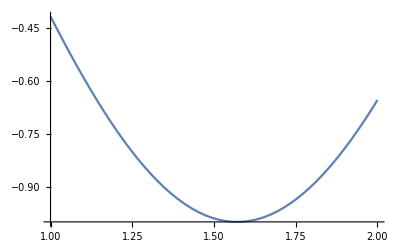

```mathematica
Plot[F[x], {x, 1, 2}]
```

```mathematica
Solve[F'[x], x]
```

Solve::naqs: -4 Cos[x] Sin[x] is not a quantified system of equations and inequalities.

Solve[-4 Cos[x] Sin[x],x]

```mathematica
F'[x]
```

-4 Cos[x] Sin[x]

```mathematica
Solve[F[x] == 0, x]
```

{{}}

```mathematica
Solve[F'[x]==0, x]
```

```mathematica
{{x->ConditionalExpression[2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]},{x->ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}
```

```mathematica
N[%]
```

{{x→ConditionalExpression[6.28319 C[1],C[1]∈Integers]},{x→ConditionalExpression[-1.5708+6.28319 C[1],C[1]∈Integers]},{x→ConditionalExpression[1.5708+6.28319 C[1],C[1]∈Integers]},{x→ConditionalExpression[3.14159+6.28319 C[1],C[1]∈Integers]}}

```mathematica
F[x]
```

0

```mathematica
H[x_]:=(Cos[x])^2-(Sin[x])^2
```

```mathematica
Solve[F'[x]==0,x]
```

{{x→ConditionalExpression[2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[-π/2+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[π/2+2 π C[1],C[1]∈Integers]},{x→ConditionalExpression[π+2 π C[1],C[1]∈Integers]}}

```mathematica
H[x]
```

Cos[x]^2-Sin[x]^2

```mathematica
FindRoot[H'[x] == 0, {x, 1, 2}]
```

{x→1.5708}

```mathematica
H[1.5708]
```

-1.

```mathematica
FindRoot[H'[x] == 0, {x, 3, 4}]
```

{x→3.14159}

```mathematica
H[3.14159]
```

1.

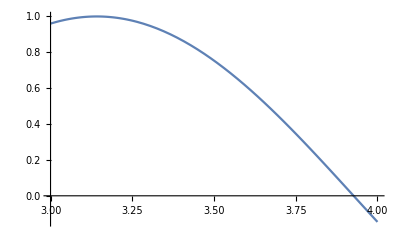

```mathematica
Plot[H[x], {x, 3, 4}]
```

```mathematica
H'[π/4]
```

-2

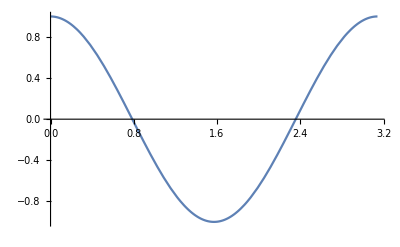

```mathematica
Plot[H[x], {x, 0, π}]
```

```mathematica
H[π/4]
```

0

```mathematica
p[x_]:=-2(x-π/4)
```

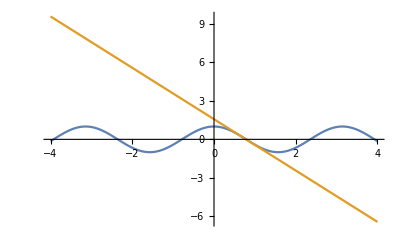

```mathematica
Plot[{H[x], p[x]}, {x, -4, 4}]
```

```mathematica
H[π/4]
```

0

```mathematica
H[x]
```

Cos[x]^2-Sin[x]^2

```mathematica
p[x]
```

-2 (-π/4+x)

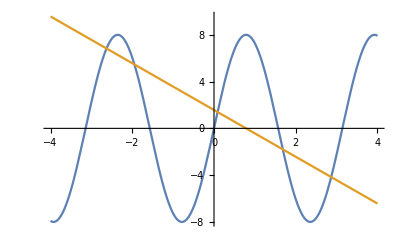

```mathematica
Plot[{H'''[x], p[x]}, {x, -4, 4}]
```

```mathematica
p[x_]:=x^4+34x^3+31x^2+2
```

```mathematica
p[x]
```

2+31 x^2+34 x^3+x^4

```mathematica
h[x_]:=x^4-36x^3+25x+6
```

```mathematica
h[x]
```

6+25 x-36 x^3+x^4

```mathematica
FindRoot[h[x]==p[x], {x, -1, 1}]
```

{x→-0.8}

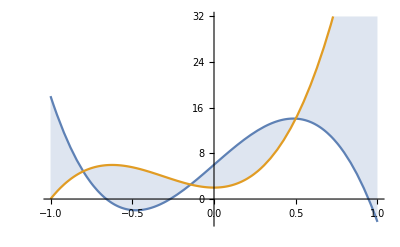

```mathematica
Plot[{h[x], p[x]}, {x, -1, 1}, Filling->{1->{2}}]
```

```mathematica
Solve[h[x]==p[x], x]
```

{{x→-4/5},{x→-1/7},{x→1/2}}

```mathematica
∫_(-4/5)^(1/2) Abs[h[x]-p[x]]ⅆx
```

25721821/4116000

```mathematica
N[%]
```

6.24923

```mathematica
a[n_]:=If[n==1, 1, a[n - 1] + 4n]
```

```mathematica
Table[a[n], {n, 1, 7}]
```

{1,9,21,37,57,81,109}

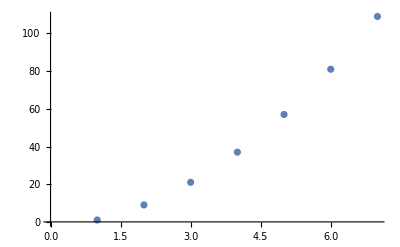

```mathematica
ListPlot[Table[a[n], {n, 1, 7}]]
```

```mathematica
RSolve[{a[n]==a[n-1]+4n,a[1]==1},a[n],n]
```

{{a[n]→-3+2 n+2 n^2}}

```mathematica
Clear[a]
```

```mathematica
g[x_]:=8x^5+3x^4-20x^3-2x^2+6x-1
```

```mathematica
g[x]
```

-1+6 x-2 x^2-20 x^3+3 x^4+8 x^5

```mathematica
Biseccion[f_,{a_,b_,n_}]:=Module[{an,bn,xn},an=a;bn=b;
For[i=1,i≤n,i++,xn=(an+bn)/2;
If[f[xn]==0, Break[],
If[f[an]*f[xn]<0, bn= xn,
If[f[xn]*f[bn]<0, an= xn]]]];
SetPrecision[xn,20]]
```

```mathematica
CotaBiseccion[a_,b_,n_]:=N[(b-a)/2^(n+1)]
```

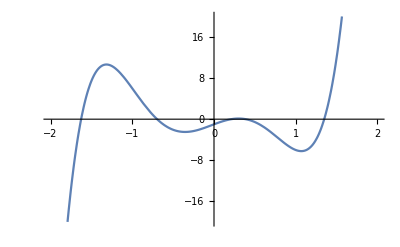

```mathematica
Plot[g[x], {x, -2, 2}, PlotRange->{-20, 20}]
```

```mathematica
Reduce[CotaBiseccion[0,1,n]<10^(-5),n,Reals]
```

Reduce::ratnz: Reduce was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

n>15.6096

```mathematica
Biseccion[g',{0,1,15.6096}]
```

0.301483154296875

```mathematica
Newton[f_,x0_,n_]:=Module[{xn},
xn=x0;
For[i=1,i≤n,i++,
xn=SetPrecision[xn-f[xn]/f'[xn],26];
Print[ "Iteración: ", i , "   Aproximación: ", 
SetPrecision[xn,26]]];
]
```

```mathematica
NewtonW[f_,x0_,epsilon_]:=Module[{xn,error,j},
xn=x0;
error=100;
j=0;
While[error>epsilon,{
xn1=SetPrecision[xn-f[xn]/f'[xn],25];
error=SetPrecision[Abs[xn1-xn],25];
xn=xn1 ;
j=j+1;
Print[ "iteración: ",  j , "  Aproximación: " , 
SetPrecision[xn1,25]]
}];
]
```

```mathematica
Newton[g',0.301483,3]
```

Iteración: 1   Aproximación: 0.30147780267911922225110288

Iteración: 2   Aproximación: 0.30147780265641650016856809

Iteración: 3   Aproximación: 0.30147780265641650016813489

```mathematica
FindRoot[g'[x],{x,0,1}, WorkingPrecision->15]
```

{x→0.301477802656209}